Some extracurricular practice junk up at the top of this section. For the first actual problem, see the orange cell below, numbered 1.

```mathematica
grating=DSolve[x^2 y''[x]+1.5 x y'[x]-0.5 y[x]==0,y[x],x]
```

{{y[x]→x^(0.5+0. ⅈ) C[1]+x^(-1.+0. ⅈ) C[2]}}

```mathematica
grid=Simplify[grating]
```

{{y[x]→(x^1.5 C[1]+C[2])/x^1.}}

```mathematica
Apart[grid]
```

{{y[x]→x^0.5 C[1]+C[2]/x^1.}}

Cauchy-Euler equation. The auxilary equation is m^2+0.5 m-0.5==0

```mathematica
Solve[m^2+0.5 m-0.5==0,m]
```

{{m→-1.},{m→0.5}}

Numbered line (1) on p. 71 goes like this: x^2 y''+a x y'+b y=0

Numbered line (2) on p. 71 goes like this: m^2+(a-1)m+b=0

1. Double root. Verify directly by substitution that x^((1-1)/2)Log[x] is a solution of (1) if (2) has a double root, but x^m_1Log[x] and x^m_2Log[x] are not solutions of (1) if the roots m_1 and m_2 of (2) are different.

```mathematica
ClearAll["Global`*"]
```

Solving (2) might be recommended.

```mathematica
Solve[m^2+(a-1) m+b==0,m]
```

{{m→1/2 (1-a-√(1-2 a+a^2-4 b))},{m→1/2 (1-a+√(1-2 a+a^2-4 b))}}

The above lists the two possible roots to (2). A double root would mean they’re equal.

```mathematica
Solve[(-√((1-a)^2-4 b))==(√((1-a)^2-4 b)),a]
```

{{a→1-2 √b},{a→1+2 √b}}

So it looks like (2) has a double root under two circumstances. And the relationship between a and b has also been established (call it ‘Rel’). Now it is time to look at the problem’s proposed sol’n.

```mathematica
y[x_]:=x^((1-a)/2) Log[x]
```

```mathematica
cran=FullSimplify[x^2 y''[x]+a x y'[x]+b y[x]]
```

-1/4 ((-1+a)^2-4 b) x^(1/2-a/2) Log[x]

```mathematica
Simplify[cran/.a->(1-2 √b)]
```

0

```mathematica
Simplify[cran/.a->(1+2 √b)]
```

0

I think I have done what the first part of the problem asked: if (2) has a double root, a certain relationship ‘Rel’ exists between the coefficients a and b in the double root. The proposed sol’n only incorporates one of the coefficients, but the candidate equation does have both, and after substituting the proposed sol’n into the candidate equation and analyzing the resulting wreckage, the relationship ‘Rel’ is found to be present. In other words, invoking ‘Rel’ proves the proposed sol’n to be an actual sol’n.

For the second part of the problem. If the roots of (2) are not equal, it would imply that m_1=1/2(1-a-√((1-a)^2-4 b)) !=m_2=1/2(1-a+√((1-a)^2-4 b)). It seems obvious that the exclamation point cannot be removed by squaring both sides! However, I don’t see what is wrong with multiplying both sides (of the pertinent sub-expressions) by the same quantity, e.g. √((1-a)^2-4 b).

```mathematica
-((1-a)^2-4 b)!=((1-a)^2-4 b)
```

-(1-a)^2+4 b≠(1-a)^2-4 b

```mathematica
8 b≠2 (1-a)^2
```

```mathematica
4 b≠(1-a)^2
```

But in the expansion of cran something very much like this came up.  What if I look at

```mathematica
Simplify[(1-a)^2==(a-1)^2]
```

```mathematica
True
```

Let me bring cran back.

```mathematica
cran
```

-1/4 ((-1+a)^2-4 b) x^(1/2-a/2) Log[x]

I contend that having the expression inside parentheses above, i.e. ((-1+a)^2-4 b), equal to zero is necessary for cran to go to zero, and, backtracking a few steps, this only happens if the roots are equal. This line of reasoning does not manipulate the specific proposed sol’ns, however. Incidentally, there is no text answer for this problem.

3.  5 x^2 y''+23 x y'+16.2 y = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
doxy={5 x^2 y''[x]+23 x y'[x]+16.2 y[x]==0}
plat=DSolve[doxy,y,x]
```

{16.2 y[x]+23 x y'[x]+5 x^2 y''[x]==0}

{{y→Function[{x},C[1]/x^1.8+(1.8 C[2] Log[x])/x^1.8]}}

```mathematica
gerz=plat[[1,1,2,2]]
```

C[1]/x^1.8+(1.8 C[2] Log[x])/x^1.8

```mathematica
derz=gerz/.{C[1]->c1,C[2]->c2}
```

c1/x^1.8+(1.8 c2 Log[x])/x^1.8

The above answer matches the text. Here 1.8*c2 equals the text answer constant c_2.

```mathematica
lint[x_,c1_,c2_]:=derz
```

```mathematica
TableForm[Table[{x,c1,c2,derz},{x,4},{c1,-1,1},{c2,-3,3,.25}],TableHeadings->{{},{"c1=-1","c1=0 ","c1=1"}}]
```

| c1=-1 | c1=0  | c1=1
 | 1 | -1 | -3. | -1.
1 | -1 | -2.75 | -1.
1 | -1 | -2.5 | -1.
1 | -1 | -2.25 | -1.
1 | -1 | -2. | -1.
1 | -1 | -1.75 | -1.
1 | -1 | -1.5 | -1.
1 | -1 | -1.25 | -1.
1 | -1 | -1. | -1.
1 | -1 | -0.75 | -1.
1 | -1 | -0.5 | -1.
1 | -1 | -0.25 | -1.
1 | -1 | 0. | -1.
1 | -1 | 0.25 | -1.
1 | -1 | 0.5 | -1.
1 | -1 | 0.75 | -1.
1 | -1 | 1. | -1.
1 | -1 | 1.25 | -1.
1 | -1 | 1.5 | -1.
1 | -1 | 1.75 | -1.
1 | -1 | 2. | -1.
1 | -1 | 2.25 | -1.
1 | -1 | 2.5 | -1.
1 | -1 | 2.75 | -1.
1 | -1 | 3. | -1. | 1 | 0 | -3. | 0.
1 | 0 | -2.75 | 0.
1 | 0 | -2.5 | 0.
1 | 0 | -2.25 | 0.
1 | 0 | -2. | 0.
1 | 0 | -1.75 | 0.
1 | 0 | -1.5 | 0.
1 | 0 | -1.25 | 0.
1 | 0 | -1. | 0.
1 | 0 | -0.75 | 0.
1 | 0 | -0.5 | 0.
1 | 0 | -0.25 | 0.
1 | 0 | 0. | 0.
1 | 0 | 0.25 | 0.
1 | 0 | 0.5 | 0.
1 | 0 | 0.75 | 0.
1 | 0 | 1. | 0.
1 | 0 | 1.25 | 0.
1 | 0 | 1.5 | 0.
1 | 0 | 1.75 | 0.
1 | 0 | 2. | 0.
1 | 0 | 2.25 | 0.
1 | 0 | 2.5 | 0.
1 | 0 | 2.75 | 0.
1 | 0 | 3. | 0. | 1 | 1 | -3. | 1.
1 | 1 | -2.75 | 1.
1 | 1 | -2.5 | 1.
1 | 1 | -2.25 | 1.
1 | 1 | -2. | 1.
1 | 1 | -1.75 | 1.
1 | 1 | -1.5 | 1.
1 | 1 | -1.25 | 1.
1 | 1 | -1. | 1.
1 | 1 | -0.75 | 1.
1 | 1 | -0.5 | 1.
1 | 1 | -0.25 | 1.
1 | 1 | 0. | 1.
1 | 1 | 0.25 | 1.
1 | 1 | 0.5 | 1.
1 | 1 | 0.75 | 1.
1 | 1 | 1. | 1.
1 | 1 | 1.25 | 1.
1 | 1 | 1.5 | 1.
1 | 1 | 1.75 | 1.
1 | 1 | 2. | 1.
1 | 1 | 2.25 | 1.
1 | 1 | 2.5 | 1.
1 | 1 | 2.75 | 1.
1 | 1 | 3. | 1.
 | 2 | -1 | -3. | -1.36207
2 | -1 | -2.75 | -1.27249
2 | -1 | -2.5 | -1.18292
2 | -1 | -2.25 | -1.09334
2 | -1 | -2. | -1.00377
2 | -1 | -1.75 | -0.914195
2 | -1 | -1.5 | -0.824621
2 | -1 | -1.25 | -0.735047
2 | -1 | -1. | -0.645472
2 | -1 | -0.75 | -0.555898
2 | -1 | -0.5 | -0.466323
2 | -1 | -0.25 | -0.376749
2 | -1 | 0. | -0.287175
2 | -1 | 0.25 | -0.1976
2 | -1 | 0.5 | -0.108026
2 | -1 | 0.75 | -0.0184513
2 | -1 | 1. | 0.0711231
2 | -1 | 1.25 | 0.160697
2 | -1 | 1.5 | 0.250272
2 | -1 | 1.75 | 0.339846
2 | -1 | 2. | 0.429421
2 | -1 | 2.25 | 0.518995
2 | -1 | 2.5 | 0.60857
2 | -1 | 2.75 | 0.698144
2 | -1 | 3. | 0.787718 | 2 | 0 | -3. | -1.07489
2 | 0 | -2.75 | -0.985319
2 | 0 | -2.5 | -0.895744
2 | 0 | -2.25 | -0.80617
2 | 0 | -2. | -0.716595
2 | 0 | -1.75 | -0.627021
2 | 0 | -1.5 | -0.537446
2 | 0 | -1.25 | -0.447872
2 | 0 | -1. | -0.358298
2 | 0 | -0.75 | -0.268723
2 | 0 | -0.5 | -0.179149
2 | 0 | -0.25 | -0.0895744
2 | 0 | 0. | 0.
2 | 0 | 0.25 | 0.0895744
2 | 0 | 0.5 | 0.179149
2 | 0 | 0.75 | 0.268723
2 | 0 | 1. | 0.358298
2 | 0 | 1.25 | 0.447872
2 | 0 | 1.5 | 0.537446
2 | 0 | 1.75 | 0.627021
2 | 0 | 2. | 0.716595
2 | 0 | 2.25 | 0.80617
2 | 0 | 2.5 | 0.895744
2 | 0 | 2.75 | 0.985319
2 | 0 | 3. | 1.07489 | 2 | 1 | -3. | -0.787718
2 | 1 | -2.75 | -0.698144
2 | 1 | -2.5 | -0.60857
2 | 1 | -2.25 | -0.518995
2 | 1 | -2. | -0.429421
2 | 1 | -1.75 | -0.339846
2 | 1 | -1.5 | -0.250272
2 | 1 | -1.25 | -0.160697
2 | 1 | -1. | -0.0711231
2 | 1 | -0.75 | 0.0184513
2 | 1 | -0.5 | 0.108026
2 | 1 | -0.25 | 0.1976
2 | 1 | 0. | 0.287175
2 | 1 | 0.25 | 0.376749
2 | 1 | 0.5 | 0.466323
2 | 1 | 0.75 | 0.555898
2 | 1 | 1. | 0.645472
2 | 1 | 1.25 | 0.735047
2 | 1 | 1.5 | 0.824621
2 | 1 | 1.75 | 0.914195
2 | 1 | 2. | 1.00377
2 | 1 | 2.25 | 1.09334
2 | 1 | 2.5 | 1.18292
2 | 1 | 2.75 | 1.27249
2 | 1 | 3. | 1.36207
 | 3 | -1 | -3. | -0.95956
3 | -1 | -2.75 | -0.891131
3 | -1 | -2.5 | -0.822702
3 | -1 | -2.25 | -0.754273
3 | -1 | -2. | -0.685845
3 | -1 | -1.75 | -0.617416
3 | -1 | -1.5 | -0.548987
3 | -1 | -1.25 | -0.480558
3 | -1 | -1. | -0.41213
3 | -1 | -0.75 | -0.343701
3 | -1 | -0.5 | -0.275272
3 | -1 | -0.25 | -0.206843
3 | -1 | 0. | -0.138415
3 | -1 | 0.25 | -0.0699858
3 | -1 | 0.5 | -0.00155702
3 | -1 | 0.75 | 0.0668717
3 | -1 | 1. | 0.135301
3 | -1 | 1.25 | 0.203729
3 | -1 | 1.5 | 0.272158
3 | -1 | 1.75 | 0.340587
3 | -1 | 2. | 0.409016
3 | -1 | 2.25 | 0.477444
3 | -1 | 2.5 | 0.545873
3 | -1 | 2.75 | 0.614302
3 | -1 | 3. | 0.682731 | 3 | 0 | -3. | -0.821145
3 | 0 | -2.75 | -0.752716
3 | 0 | -2.5 | -0.684288
3 | 0 | -2.25 | -0.615859
3 | 0 | -2. | -0.54743
3 | 0 | -1.75 | -0.479001
3 | 0 | -1.5 | -0.410573
3 | 0 | -1.25 | -0.342144
3 | 0 | -1. | -0.273715
3 | 0 | -0.75 | -0.205286
3 | 0 | -0.5 | -0.136858
3 | 0 | -0.25 | -0.0684288
3 | 0 | 0. | 0.
3 | 0 | 0.25 | 0.0684288
3 | 0 | 0.5 | 0.136858
3 | 0 | 0.75 | 0.205286
3 | 0 | 1. | 0.273715
3 | 0 | 1.25 | 0.342144
3 | 0 | 1.5 | 0.410573
3 | 0 | 1.75 | 0.479001
3 | 0 | 2. | 0.54743
3 | 0 | 2.25 | 0.615859
3 | 0 | 2.5 | 0.684288
3 | 0 | 2.75 | 0.752716
3 | 0 | 3. | 0.821145 | 3 | 1 | -3. | -0.682731
3 | 1 | -2.75 | -0.614302
3 | 1 | -2.5 | -0.545873
3 | 1 | -2.25 | -0.477444
3 | 1 | -2. | -0.409016
3 | 1 | -1.75 | -0.340587
3 | 1 | -1.5 | -0.272158
3 | 1 | -1.25 | -0.203729
3 | 1 | -1. | -0.135301
3 | 1 | -0.75 | -0.0668717
3 | 1 | -0.5 | 0.00155702
3 | 1 | -0.25 | 0.0699858
3 | 1 | 0. | 0.138415
3 | 1 | 0.25 | 0.206843
3 | 1 | 0.5 | 0.275272
3 | 1 | 0.75 | 0.343701
3 | 1 | 1. | 0.41213
3 | 1 | 1.25 | 0.480558
3 | 1 | 1.5 | 0.548987
3 | 1 | 1.75 | 0.617416
3 | 1 | 2. | 0.685845
3 | 1 | 2.25 | 0.754273
3 | 1 | 2.5 | 0.822702
3 | 1 | 2.75 | 0.891131
3 | 1 | 3. | 0.95956
 | 4 | -1 | -3. | -0.699833
4 | -1 | -2.75 | -0.648386
4 | -1 | -2.5 | -0.596939
4 | -1 | -2.25 | -0.545492
4 | -1 | -2. | -0.494045
4 | -1 | -1.75 | -0.442598
4 | -1 | -1.5 | -0.391151
4 | -1 | -1.25 | -0.339704
4 | -1 | -1. | -0.288257
4 | -1 | -0.75 | -0.23681
4 | -1 | -0.5 | -0.185363
4 | -1 | -0.25 | -0.133916
4 | -1 | 0. | -0.0824692
4 | -1 | 0.25 | -0.0310223
4 | -1 | 0.5 | 0.0204247
4 | -1 | 0.75 | 0.0718717
4 | -1 | 1. | 0.123319
4 | -1 | 1.25 | 0.174766
4 | -1 | 1.5 | 0.226213
4 | -1 | 1.75 | 0.27766
4 | -1 | 2. | 0.329107
4 | -1 | 2.25 | 0.380554
4 | -1 | 2.5 | 0.432001
4 | -1 | 2.75 | 0.483448
4 | -1 | 3. | 0.534895 | 4 | 0 | -3. | -0.617364
4 | 0 | -2.75 | -0.565917
4 | 0 | -2.5 | -0.51447
4 | 0 | -2.25 | -0.463023
4 | 0 | -2. | -0.411576
4 | 0 | -1.75 | -0.360129
4 | 0 | -1.5 | -0.308682
4 | 0 | -1.25 | -0.257235
4 | 0 | -1. | -0.205788
4 | 0 | -0.75 | -0.154341
4 | 0 | -0.5 | -0.102894
4 | 0 | -0.25 | -0.051447
4 | 0 | 0. | 0.
4 | 0 | 0.25 | 0.051447
4 | 0 | 0.5 | 0.102894
4 | 0 | 0.75 | 0.154341
4 | 0 | 1. | 0.205788
4 | 0 | 1.25 | 0.257235
4 | 0 | 1.5 | 0.308682
4 | 0 | 1.75 | 0.360129
4 | 0 | 2. | 0.411576
4 | 0 | 2.25 | 0.463023
4 | 0 | 2.5 | 0.51447
4 | 0 | 2.75 | 0.565917
4 | 0 | 3. | 0.617364 | 4 | 1 | -3. | -0.534895
4 | 1 | -2.75 | -0.483448
4 | 1 | -2.5 | -0.432001
4 | 1 | -2.25 | -0.380554
4 | 1 | -2. | -0.329107
4 | 1 | -1.75 | -0.27766
4 | 1 | -1.5 | -0.226213
4 | 1 | -1.25 | -0.174766
4 | 1 | -1. | -0.123319
4 | 1 | -0.75 | -0.0718717
4 | 1 | -0.5 | -0.0204247
4 | 1 | -0.25 | 0.0310223
4 | 1 | 0. | 0.0824692
4 | 1 | 0.25 | 0.133916
4 | 1 | 0.5 | 0.185363
4 | 1 | 0.75 | 0.23681
4 | 1 | 1. | 0.288257
4 | 1 | 1.25 | 0.339704
4 | 1 | 1.5 | 0.391151
4 | 1 | 1.75 | 0.442598
4 | 1 | 2. | 0.494045
4 | 1 | 2.25 | 0.545492
4 | 1 | 2.5 | 0.596939
4 | 1 | 2.75 | 0.648386
4 | 1 | 3. | 0.699833

According to above table, the general sol’n is a specific sol’n only when c1=0. There are a number of instances shown for various values of c2. The plot below shows these functions, each of which is a particular sol’n (when x =1).

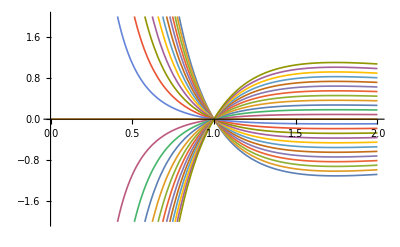

```mathematica
plot3=Plot[Evaluate[Table[lint[x,c1,c2],{c1,0,0},{c2,-3,3,.25}]],{x,0,2},PlotRange->{-2,2},PlotStyle->Thickness[0.003]]
```

What happened? The sol’n found by DSolve matches the text’s answer. However, the original DE only vanishes when x=1&&c1=0.

5.  4 x^2 y''+5y=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
tier={4 x^2 y''[x]+5 y[x]==0}
```

{5 y[x]+4 x^2 y''[x]==0}

```mathematica
cins=DSolve[tier,y,x]
```

{{y→Function[{x},√x C[2] Cos[Log[x]]+√x C[1] Sin[Log[x]]]}}

The above cell matches the text answer.

```mathematica
Simplify[tier/.cins]
```

{{True}}

In the above case the sol’n checks out with Mathematica as well as matching the text’s answer.

7.  (x^2 D^2-4x D +6 I)y=C

```mathematica
ClearAll["Global`*"]
```

```mathematica
hol={x^2 y''[x]-4 x y'[x]+6 y[x]==c}
dea=DSolve[hol,y,x]
```

{6 y[x]-4 x y'[x]+x^2 y''[x]==c}

{{y→Function[{x},c/6+x^2 C[1]+x^3 C[2]]}}

```mathematica
Simplify[hol/.dea]
```

{{True}}

The above answer matches the text’s, with the original rhs c constant equaling zero in the text answer.

9.  (x^2 D = 0.2 x D + 0.36 I)y = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
reg={x^2 y''[x]-0.2 x y'[x]+0.36 y[x]==0}
dirk=DSolve[reg,y,x]
```

{0.36 y[x]-0.2 x y'[x]+x^2 y''[x]==0}

{{y→Function[{x},x^0.6 C[1]+0.6 x^0.6 C[2] Log[x]]}}

```mathematica
Chop[Simplify[reg/.dirk],10^-16]
```

{{True}}

The above answer matches the text’s. However, the checking step does not work cleanly. The default tolerance for Chop is 10^-10, and in this case 10^-16 will work. But an exact answer would be preferred.

11. (x^2 D^2-3 x D+10 I)y=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
deam={x^2 y''[x]-3 x y'[x]+10 y[x]==0}
vre=DSolve[deam,y,x]
```

{10 y[x]-3 x y'[x]+x^2 y''[x]==0}

{{y→Function[{x},x^2 C[2] Cos[√6 Log[x]]+x^2 C[1] Sin[√6 Log[x]]]}}

```mathematica
Simplify[deam/.vre]
```

{{True}}

In this case the substitution worked cleanly. The answer also matches the text’s.

12 - 19 Initial value problem
Solve and graph the solution.

13. x^2 y''+3 x y'+0.75y=0, y[1]=1,y'[1]=-1.5

```mathematica
ClearAll["Global`*"]
```

```mathematica
non={x^2 y''[x]+3 x y'[x]+0.75 y[x]==0,y[1]==1,y'[1]==-1.5}
by=DSolve[non,y,x]
```

{0.75 y[x]+3 x y'[x]+x^2 y''[x]==0,y[1]==1,y'[1]==-1.5}

{{y→Function[{x},(1. x^0.5+8.88178×10^-16 x^1.5)/x^2.]}}

```mathematica
rek=Chop[by,10^-15]
```

{{y→Function[{x},(1. x^0.5+0 x^1.5)/x^2.]}}

The posed floating point format in the problem created a slight haze which made Chop necessary. Allowing this, the answer matches the text’s.

```mathematica
Simplify[non/.rek]
```

{{True,True,True}}

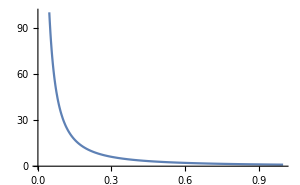

```mathematica
Plot[y[x]/.rek,{x,0,1},PlotRange->{0,100},ImageSize->300]
```

15. x^2 y''+3 x y+y=0, y[1]=3.6, y'[1]=0.4

```mathematica
ClearAll["Global`*"]
```

```mathematica
hote={x^2 y''[x]+3 x y'[x]+y[x]==0,y[1]==3.6,y'[1]==0.4}
deli=DSolve[hote,y,x]
```

{y[x]+3 x y'[x]+x^2 y''[x]==0,y[1]==3.6,y'[1]==0.4}

{{y→Function[{x},(4. (0.9+1. Log[x]))/x]}}

```mathematica
Simplify[hote/.deli]
```

{{True,True,True}}

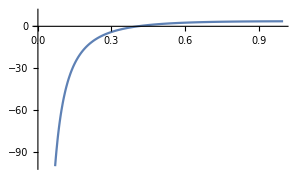

```mathematica
Plot[y[x]/.deli,{x,0,1},PlotRange->{-100,10},ImageSize->300]
```

The answer matches the text’s.

17.  (x^2 D^2+x D + I)y=0, y[1]=1,y'[1]=1

```mathematica
ClearAll["Global`*"]
```

```mathematica
zog={x^2 y''[x]+ x y'[x]+y[x]==0,y[1]==1,y'[1]==1}
nilt=DSolve[zog,y,x]
```

{y[x]+x y'[x]+x^2 y''[x]==0,y[1]==1,y'[1]==1}

{{y→Function[{x},Cos[Log[x]]+Sin[Log[x]]]}}

```mathematica
Simplify[zog/.nilt]
```

{{True,True,True}}

The answer matches the text’s.

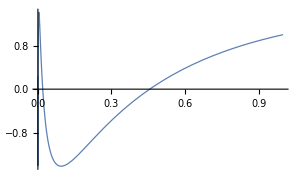

```mathematica
Plot[y[x]/.nilt,{x,-1,1},PlotRange->All,ImageSize->300,PlotStyle->Thickness[0.003]]
```

19.  (x^2 D^2-x D -15 I)y=0, y[1]=0.1, y'[1]=-4.5

```mathematica
ClearAll["Global`*"]
```

```mathematica
wer={x^2 y''[x]-x y'[x]-15 y[x]==0,y[1]==0.1,y'[1]==-4.5}
jip=DSolve[wer,y,x]
```

{-15 y[x]-x y'[x]+x^2 y''[x]==0,y[1]==0.1,y'[1]==-4.5}

{{y→Function[{x},-(0.525 (-1.19048+1. x^8))/x^3]}}

```mathematica
Simplify[wer/.jip]
```

{{x==0,True,True}}

The initial value points are verified.  However, the general sol’n is still under a shadow.

```mathematica
ard=jip[[1,1,2,2]]
```

-(0.525 (-1.19048+1. x^8))/x^3

```mathematica
poi=ExpandNumerator[ard]
```

(0.625-0.525 x^8)/x^3

```mathematica
deke=Expand[poi]
```

0.625/x^3-0.525 x^5

The above form matches the text’s answer. Below is a series of steps to check the sol’n ‘by hand’.

```mathematica
mot[x_]:=0.625/x^3-0.5249999999999999 x^5
```

```mathematica
mot1=D[mot[x],x]
```

-1.875/x^4-2.625 x^4

```mathematica
mot2=D[mot[x],{x,2}]
```

7.5/x^5-10.5 x^3

```mathematica
Simplify[-15 mot[x]-x mot'[x]+x^2 mot''[x]]
```

0.

The sol’n is checked ‘by hand’ and found to be correct.

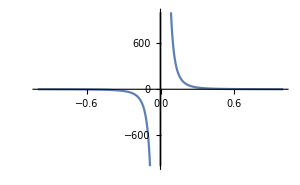

```mathematica
Plot[poi,{x,-1,1},PlotRange->{-1000,1000},ImageSize->300]
```

The vertical line in the plot is an artifact, as the function is undefined at x=0.